# 3 body Hamiltonian

#### Definitions

```mathematica
Clear[b]
```

```mathematica
αβγ[b_]:={-((b[[1]]+b[[2]])/4+b[[3]]),-(b[[1]]+b[[2]]),(b[[1]]-b[[2]])/2}
```

```mathematica
Expand[α β-γ^2/.{α->-((b1+b2)/4+b3),β->-(b1+b2),γ->(b1-b2)/2}]
```

b1 b2+b1 b3+b2 b3

```mathematica
pow=3;
```

```mathematica
Solve[{α==-((b1+b2)/4+b3),β==-(b1+b2),γ==(b1-b2)/2},{b1,b2,b3}]
```

{{b1→1/2 (-β+2 γ),b2→1/2 (-β-2 γ),b3→-α+β/4}}

```mathematica
int[α_]:=(√(2/π)NIntegrate[r^2 Exp[-r^2/2]/Cosh[r α^(-1/2)]^pow,{r,0,∞}])
```

```mathematica
intp[α_]:=(√(2/π)α^(3/2) NIntegrate[r^2 Exp[-α r^2/2]/Cosh[r^pow],{r,0,∞}])
```

Check this integral for α very large (should be one)

```mathematica
int[99999999]
```

1.

```mathematica
Clear[α]
```

```mathematica
as=AsymptoticIntegrate[√(2/π)r^2 Exp[-r^2/2]/Cosh[r α^(-1/2)]^pow,{r,0,∞},{α,∞,30}];
```

```mathematica
ass=PadeApproximant[as,{α,∞,{14,15}}];
```

```mathematica
ass=N[ass]
```

(1.+(3.09397×10^12)/α^14+(6.04228×10^13)/α^13+(1.63122×10^14)/α^12+(1.4407×10^14)/α^11+(6.39673×10^13)/α^10+(1.68681×10^13)/α^9+(2.87095×10^12)/α^8+(3.3006×10^11)/α^7+(2.62477×10^10)/α^6+(1.45562×10^9)/α^5+(5.59408×10^7)/α^4+(1.45508×10^6)/α^3+24351.9/α^2+235.773/α)/(1.+(6.72897×10^13)/α^15+(4.62×10^14)/α^14+(9.39567×10^14)/α^13+(8.62613×10^14)/α^12+(4.41909×10^14)/α^11+(1.4103×10^14)/α^10+(2.98657×10^13)/α^9+(4.35876×10^12)/α^8+(4.48142×10^11)/α^7+(3.27911×10^10)/α^6+(1.70705×10^9)/α^5+(6.2482×10^7)/α^4+(1.56458×10^6)/α^3+25412.5/α^2+240.273/α)

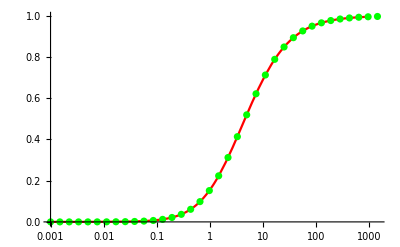

```mathematica
Block[{α},Show[{LogLinearPlot[N[ass],{α,0.001,1000}, PlotStyle->Red],ListLogLinearPlot[Table[{α=0.001 1.5^i,int[α]},{i,0,35}],PlotStyle->Green]},PlotRange->All]]
```

```mathematica
int[α_]=ass
```

(1.+(3.09397×10^12)/α^14+(6.04228×10^13)/α^13+(1.63122×10^14)/α^12+(1.4407×10^14)/α^11+(6.39673×10^13)/α^10+(1.68681×10^13)/α^9+(2.87095×10^12)/α^8+(3.3006×10^11)/α^7+(2.62477×10^10)/α^6+(1.45562×10^9)/α^5+(5.59408×10^7)/α^4+(1.45508×10^6)/α^3+24351.9/α^2+235.773/α)/(1.+(6.72897×10^13)/α^15+(4.62×10^14)/α^14+(9.39567×10^14)/α^13+(8.62613×10^14)/α^12+(4.41909×10^14)/α^11+(1.4103×10^14)/α^10+(2.98657×10^13)/α^9+(4.35876×10^12)/α^8+(4.48142×10^11)/α^7+(3.27911×10^10)/α^6+(1.70705×10^9)/α^5+(6.2482×10^7)/α^4+(1.56458×10^6)/α^3+25412.5/α^2+240.273/α)

```mathematica
int2[α_]:=(1/3/√(π/2)NIntegrate[r^4 Exp[-r^2/2]/Cosh[r α^(-1/2)]^pow,{r,0,∞}])
```

```mathematica
as2=AsymptoticIntegrate[1/3/√(π/2)r^4 Exp[-r^2/2]/Cosh[r α^(-1/2)]^pow,{r,0,∞},{α,∞,30}];
```

```mathematica
ass2=PadeApproximant[as2,{α,∞,{14,15}}];
```

```mathematica
ass2=N[ass2]
```

(1.-(1.79849×10^11)/α^14+(4.18296×10^12)/α^13+(3.87766×10^13)/α^12+(5.18582×10^13)/α^11+(2.90382×10^13)/α^10+(8.93517×10^12)/α^9+(1.7037×10^12)/α^8+(2.14296×10^11)/α^7+(1.83775×10^10)/α^6+(1.08923×10^9)/α^5+(4.44943×10^7)/α^4+(1.22642×10^6)/α^3+21721.2/α^2+222.557/α)/(1.+(1.01826×10^14)/α^15+(5.02119×10^14)/α^14+(8.50887×10^14)/α^13+(7.20528×10^14)/α^12+(3.55962×10^14)/α^11+(1.11955×10^14)/α^10+(2.36567×10^13)/α^9+(3.4736×10^12)/α^8+(3.61571×10^11)/α^7+(2.69257×10^10)/α^6+(1.43323×10^9)/α^5+(5.38724×10^7)/α^4+(1.39115×10^6)/α^3+23398.5/α^2+230.057/α)

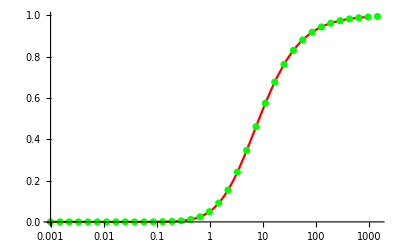

```mathematica
Block[{α},Show[{LogLinearPlot[N[ass2],{α,0.001,1000}, PlotStyle->Red],ListLogLinearPlot[Table[{α=0.001 1.5^i,int2[α]},{i,0,35}],PlotStyle->Green]},PlotRange->All]]
```

```mathematica
int2[α_]=ass2
```

(1.-(1.79849×10^11)/α^14+(4.18296×10^12)/α^13+(3.87766×10^13)/α^12+(5.18582×10^13)/α^11+(2.90382×10^13)/α^10+(8.93517×10^12)/α^9+(1.7037×10^12)/α^8+(2.14296×10^11)/α^7+(1.83775×10^10)/α^6+(1.08923×10^9)/α^5+(4.44943×10^7)/α^4+(1.22642×10^6)/α^3+21721.2/α^2+222.557/α)/(1.+(1.01826×10^14)/α^15+(5.02119×10^14)/α^14+(8.50887×10^14)/α^13+(7.20528×10^14)/α^12+(3.55962×10^14)/α^11+(1.11955×10^14)/α^10+(2.36567×10^13)/α^9+(3.4736×10^12)/α^8+(3.61571×10^11)/α^7+(2.69257×10^10)/α^6+(1.43323×10^9)/α^5+(5.38724×10^7)/α^4+(1.39115×10^6)/α^3+23398.5/α^2+230.057/α)

```mathematica
detb[b_]:=b[[1]] b[[2]]+b[[2]] b[[3]]+b[[3]]b[[1]]
```

```mathematica
dαβγ[α_,β_,γ_]:=α β -γ^2
```

```mathematica
Clear[matrixel];matrixel[b_,bp_,λ0_:1.3,debug_:False]:=Block[{α,β,γ,αp,βp,γp,bs,αs,βs,γs,ovl,kin,pot, s,arg},
arg[bs_]:=-(bs⟦2⟧ bs⟦3⟧+bs⟦1⟧ (bs⟦2⟧+bs⟦3⟧))/(bs[[1]]+bs[[2]]);
bs=b+bp;
{α,β,γ}=αβγ[b];{αp,βp,γp}=αβγ[bp]; {αs,βs,γs}=αβγ[bs];
s={-λ0(λ0+1)/2,-λ0(λ0+1)/2,-(λ0-1)(λ0)/2};
ovl=  (dαβγ[2α,2β,2γ]^(3/4)dαβγ[2αp,2βp,2γp]^(3/4))/dαβγ[αs,βs,γs]^(3/2);
kin=
3/4(3β βp αs+4 α αp βs-4(α γp^2+αp γ^2)-3(β γp^2+βp γ^2))/dαβγ[αs,βs,γs] ovl;
If[debug,Return[{ovl,kin,ovl int[arg[bs]],ovl  int[arg[RotateLeft[bs,1]]],ovl int[arg[RotateLeft[bs,2]]]}],
pot=ovl(Plus@@{s[[1]] int[arg[bs]],s[[2]] int[arg[RotateLeft[bs,1]]],s[[3]] int[arg[RotateLeft[bs,2]]]});
{ovl,kin+pot}]
]
```

#### Test

```mathematica
bt1=RandomReal[{-2,-0.1},3]
```

{-1.4279,-0.509657,-0.290181}

```mathematica
btp1=RandomReal[{-2,-0.1},3]
```

{-0.552105,-1.61542,-0.466473}

```mathematica
mel=matrixel[bt1,btp1,1.3,True]
```

{0.793211,2.48484,0.208285,0.27374,0.283904}

```mathematica
{α1,β1,γ1}=αβγ[bt1]
```

{0.77457,1.93756,-0.459121}

```mathematica
{αp1,βp1,γp1}=αβγ[btp1]
```

{1.00835,2.16753,0.531658}

```mathematica
Integrate[Exp[-α1/2 ξ^2-β1/2 η^2-γ1 ξ η],{ξ,-∞,∞},{η,-∞,∞}](dαβγ[α1,β1,γ1]^(1/2))/(2π)
```

1.

```mathematica
nrms=(√(1/(Integrate[Exp[-α1 ξ^2-β1 η^2-2γ1 ξ η],{ξ,-∞,∞},{η,-∞,∞}]Integrate[Exp[-αp1 ξ^2-βp1 η^2-2γp1 ξ η],{ξ,-∞,∞},{η,-∞,∞}])))^3;
```

Overlap

```mathematica
nrms (Integrate[Exp[-(α1+αp1)/2 ξ^2-(β1+βp1)/2 η^2-(γ1+γp1) ξ η],{ξ,-∞,∞},{η,-∞,∞}])^3/mel[[1]]
```

1.

And alternative form

```mathematica
nrms (4π ((2π)/(β1+βp1))^(3/2)Integrate[r^2 Exp[-1/2((α1+αp1)-(γ1+γp1)^2/(β1+βp1))r^2],{r,0,∞}])/mel[[1]]
```

1.

Kinetic energy

```mathematica
nrms 3 Integrate[Exp[-(α1+αp1)/2 ξ^2-(β1+βp1)/2 η^2-(γ1+γp1) ξ η],{ξ,-∞,∞},{η,-∞,∞}]^2 Integrate[Exp[-α1/2 ξ^2-β1/2 η^2-γ1 ξ η](-D[#, ξ,ξ]+-3/4 D[#, η,η])&[Exp[-αp1/2 ξ^2-βp1/2 η^2-γp1 ξ η]],{ξ,-∞,∞},{η,-∞,∞}]/mel[[2]]
```

1.

Potential

```mathematica
nrms 4 π Block[{α1,β1,γ1,αp1,βp1,γp1},Table[{α1,β1,γ1}=αβγ[RotateLeft[bt1,i-1]];
{αp1,βp1,γp1}=αβγ[RotateLeft[btp1,i-1]];(2π)^(3/2)/(β1+βp1)^(3/2)NIntegrate[r^2 Exp[-1/2((α1+αp1)-(γ1+γp1)^2/(β1+βp1))r^2]{1,1/Cosh[r]^pow},{r,0,∞}],{i,3}]]/{{mel[[1]],mel[[3]]},{mel[[1]],mel[[4]]},{mel[[1]],mel[[5]]}}
```

{{1.,1.},{1.,1.},{1.,1.}}

```mathematica
Clear[nrms,bt1,btp1,α1,β1,γ1,αp1,βp1,γp1,mel]
```

### L = 1

```mathematica
dαβγc[α_,β_,γ_,cmm_,cpp_,cmp_]:=If[γ==0.,(cmm β+cpp α-cmp 10^-9)/(α β),(cmm β+cpp α-cmp γ)/(α β-γ^2) ]
```

```mathematica
?dαβγ
```

```mathematica
Clear[ctopm];ctopm[c_]:={c[[3]],(c[[2]]-c[[1]])/2}
```

```mathematica
Clear[matrixel1];matrixel1[bc_,bcp_,λ0_:1.3,debug_:False]:=Block[{α,β,γ,αp,βp,γp,bs,αs,βs,γs,cp,cm,cpp,cpm,ovl,ovl0,kin,pot, s,v2},
bs=bc[[1]]+bcp[[1]];
{α,β,γ}=αβγ[bc[[1]]];{αp,βp,γp}=αβγ[bcp[[1]]]; {αs,βs,γs}=αβγ[bs];
{cp,cm}=ctopm[bc[[2]]];{cpp,cpm}=ctopm[bcp[[2]]];
s={-λ0(λ0+1)/2,-λ0(λ0+1)/2,-λ0(λ0-1)/2};
v2[bs_,c1i_,c2i_]:=Block[{cpi,cmi,cppi,cpmi,αsi,βsi,γsi,ϵ,δ},{αsi,βsi,γsi}=αβγ[bs];{cpi,cmi}=ctopm[c1i];{cppi,cpmi}=ctopm[c2i];δ=αsi-γsi^2/βsi;ϵ=(cmi βsi-cpi γsi)(cpmi βsi-cppi γsi)/βsi;(*Print[{c1i,c2i,αsi,βsi,γsi,δ,ϵ, cpi cppi, int[δ],int2[δ]}];*)(*(cpi cppi δ int[δ]+ ϵ int2[δ])/(cpi cppi δ +ϵ)*)(cpi cppi δ int[δ]+ ϵ int2[δ])/dαβγ[αsi,βsi,γsi]];

ovl0=  (dαβγ[2α,2β,2γ]^(3/4)dαβγ[2αp,2βp,2γp]^(3/4))/dαβγ[αs,βs,γs]^(3/2)/(dαβγc[2α,2β,2γ,cm cm,cp cp,2cm cp]^(1/2)dαβγc[2αp,2βp,2γp,cpm cpm,cpp cpp,2cpm cpp]^(1/2));
ovl=ovl0
dαβγc[α+αp,β+βp,γ+γp,cm cpm,cp cpp,cpm cp+cm cpp];
kin=
(cm cpp (8 αp^2 (β+βp) γ+3 (γ+γp) (3 βp γ^2+β γp (-2 γ+γp))+(α+αp) (6 β^2 γp-3 β βp (3 γ+γp))+4 (γ+γp) (αp γ (γ-2 γp)+3 α γp^2)-4α αp (β+βp) (γ+3 γp))+cm cpm (-3 βp (β+3 βp) γ^2-3 β (3 β+βp) γp^2+12 γ  β βp γp+8 γ γp (γ+γp)^2+3 (α+αp)(β+βp) β βp-12 (β+βp) ( αp γ^2+ α γp^2)-8 (α+αp) (β+βp)γ γp  +12α αp(β+βp)^2)+cp cpp (-3(α+αp) (3 βp γ^2+2 (β+βp) γ γp+3 β γp^2)+9(α+αp)^2 ( β βp)-12( γ^2 αp^2+α^2 γp^2)+4α αp(α+αp) (β+βp)+6 γ γp (γ+γp)^2-4α  αp (γ^2-4 γ γp+γp^2))+cp cpm (-α βp(-6 βp γ)-α βp(3 β (γ+3 γp))+3αp βp (2 βp γ-β (γ+3 γp))+4 (γ+γp) (3 αp γ^2+α γp (-2 γ+γp))+8 α^2 (β+βp) γp-4α  αp (β+βp) (3 γ+γp)+3 (γ+γp) (βp γ (γ-2 γp)+3 β γp^2)))/(4 ((α +αp) (β+βp)-(γ+γp)^2)^2)ovl0+1/2(3β βp αs+4 α αp βs-4(α γp^2+αp γ^2)-3(β γp^2+βp γ^2))/dαβγ[αs,βs,γs] ovl;
If[debug,Print[{ovl,kin,Table[ovl0  v2[RotateLeft[bs,i-1],RotateLeft[bc[[2]],i-1],RotateLeft[bcp[[2]],i-1]],{i,3}]}],pot=ovl0(Plus@@Table[ s[[i]] v2[RotateLeft[bs,i-1],RotateLeft[bc[[2]],i-1],RotateLeft[bcp[[2]],i-1]],{i,3}]);{ovl,kin+pot}]
]
```

#### Test

```mathematica
bt1=RandomReal[{-2,-0.1},3];
btp1=RandomReal[{-2,-0.1},3];
c1=RandomReal[{-2,2},2];
AppendTo[c1,-Plus@@c1];
c2=RandomReal[{-2,2},2];
AppendTo[c2,-Plus@@c2];
```

```mathematica
ctopm[{-0.3435705577369257,1.1025819656047675,-0.7590114078678418}]
```

{-0.759011,0.723076}

```mathematica
matrixel1[{bt1,c1},{btp1,c2},1.3,True]
```

{0.550913,3.92102,{0.159005,0.174315,0.276919}}

```mathematica
{α1,β1,γ1}=αβγ[bt1];
{αp1,βp1,γp1}=αβγ[btp1];
{cp1,cm1}=ctopm[c1];
{cp2,cm2}=ctopm[c2];
```

```mathematica
{c1,c2,α1+αp1,β1+βp1,γ1+γp1,cp1 cp2}
```

{{1.72274,-1.88738,0.16464},{0.31012,-1.17458,0.864458},3.86945,5.49366,0.314347,0.142324}

```mathematica
{nrm1=Integrate[(cp1  η+cm1 ξ)^2 Exp[-α1 ξ^2-β1 η^2-2γ1 ξ η],{ξ,-∞,∞},{η,-∞,∞}] Integrate[Exp[-α1 ξ^2-β1 η^2-2γ1 ξ η],{ξ,-∞,∞},{η,-∞,∞}]^2,(2π)^3 dαβγc[2α1,2β1,2γ1,cm1 cm1,cp1 cp1,2cm1 cp1]/dαβγ[2α1,2β1,2γ1]^(3/2)}
```

{2.4208,2.4208}

```mathematica
{nrm2=Integrate[(cp2 η+cm2 ξ)^2 Exp[-αp1 ξ^2-βp1 η^2-2γp1 ξ η],{ξ,-∞,∞},{η,-∞,∞}] Integrate[Exp[-αp1 ξ^2-βp1 η^2-2γp1 ξ η],{ξ,-∞,∞},{η,-∞,∞}]^2,(2π)^3 dαβγc[2αp1,2βp1,2γp1,cm2 cm2,cp2 cp2,2cm2 cp2]/dαβγ[2αp1,2βp1,2γp1]^(3/2)}
```

{1.40706,1.40706}

```mathematica
Block[{α1,β1,γ1,αp1,βp1,γp1,cp1,cm1,cp2,cm2},Table[{α1,β1,γ1}=αβγ[RotateLeft[bt1,i-1]];
{αp1,βp1,γp1}=αβγ[RotateLeft[btp1,i-1]];
{cp1,cm1}=ctopm[RotateLeft[c1,i-1]];
{cp2,cm2}=ctopm[RotateLeft[c2,i-1]];Integrate[(cp1 η+cm1 ξ)(cp2 η+cm2 ξ)Exp[-(α1+αp1)/2 ξ^2-(β1+βp1)/2 η^2-(γ1+γp1) ξ η],{ξ,-∞,∞},{η,-∞,∞}] Integrate[Exp[-(α1+αp1)/2 ξ^2-(β1+βp1)/2 η^2-(γ1+γp1) ξ η],{ξ,-∞,∞},{η,-∞,∞}]^2,{i,3}]/Sqrt[nrm1 nrm2]]
```

{0.550913,0.550913,0.550913}

```mathematica
Integrate[(cp1 η+cm1 ξ)(cp2 η+cm2 ξ)Exp[-(α1+αp1)/2 ξ^2-(β1+βp1)/2 η^2-(γ1+γp1) ξ η],{ξ,-∞,∞},{η,-∞,∞}] Integrate[Exp[-(α1+αp1)/2 ξ^2-(β1+βp1)/2 η^2-(γ1+γp1) ξ η],{ξ,-∞,∞},{η,-∞,∞}]^2
```

1.01676

```mathematica
√(1/(nrm1 nrm2)) (Integrate[Exp[-(α1+αp1)/2 ξ^2-(β1+βp1)/2 η^2-(γ1+γp1) ξ η],{ξ,-∞,∞},{η,-∞,∞}]^2 Integrate[(cp1 η +cm1 ξ)Exp[-α1/2 ξ^2-β1/2 η^2-γ1 ξ η](-D[#, ξ,ξ]-3/4 D[#, η,η])&[(cp2 η +cm2 ξ)Exp[-αp1/2 ξ^2-βp1/2 η^2-γp1 ξ η]],{ξ,-∞,∞},{η,-∞,∞}]+2Integrate[Exp[-(α1+αp1)/2 ξ^2-(β1+βp1)/2 η^2-(γ1+γp1) ξ η],{ξ,-∞,∞},{η,-∞,∞}]Integrate[(cp1 η+cm1 ξ)(cp2 η+cm2 ξ)Exp[-(α1+αp1)/2 ξ^2-(β1+βp1)/2 η^2-(γ1+γp1) ξ η],{ξ,-∞,∞},{η,-∞,∞}]Integrate[Exp[-α1/2 ξ^2-β1/2 η^2-γ1 ξ η](-D[#, ξ,ξ]-3/4 D[#, η,η])&[Exp[-αp1/2 ξ^2-βp1/2 η^2-γp1 ξ η]],{ξ,-∞,∞},{η,-∞,∞}])
```

3.92102

```mathematica
√(1/(nrm1 nrm2))4 π (2π)^(3/2)/(β1+βp1)^(5/2)NIntegrate[(cp1 cp2+((cm1(β1+βp1)-cp1(γ1+γp1))(cm2(β1+βp1)-cp2(γ1+γp1)))/(β1+βp1)1/3 r^2)r^2 Exp[-1/2((α1+αp1)-(γ1+γp1)^2/(β1+βp1))r^2] 1/Cosh[r]^pow,{r,0,∞}]
```

0.159005

```mathematica
√(1/(nrm1 nrm2))4 π Block[{α1,β1,γ1,αp1,βp1,γp1,cp1,cm1,cp2,cm2},Table[{α1,β1,γ1}=αβγ[RotateLeft[bt1,i-1]];
{αp1,βp1,γp1}=αβγ[RotateLeft[btp1,i-1]];
{cp1,cm1}=ctopm[RotateLeft[c1,i-1]];
{cp2,cm2}=ctopm[RotateLeft[c2,i-1]];(2π)^(3/2)/(β1+βp1)^(5/2)NIntegrate[(cp1 cp2+((cm1(β1+βp1)-cp1(γ1+γp1))(cm2(β1+βp1)-cp2(γ1+γp1)))/(β1+βp1)1/3 r^2)r^2 Exp[-1/2((α1+αp1)-(γ1+γp1)^2/(β1+βp1))r^2]{1,1/Cosh[r]^pow},{r,0,∞}],{i,3}]]
```

{{0.550913,0.159005},{0.550913,0.174315},{0.550913,0.276919}}

```mathematica
{0.469737223558384,1.838662992499435,{0.2936552545371748,0.302016260570959,0.21268578373289815}}
```

{0.469737,1.83866,{0.293655,0.302016,0.212686}}

## Calculation

### L=0

```mathematica
bs=Block[{t},t=Table[-0.002 3.3^i, {i,4}];Flatten[Outer[List,t,t,t],2]];
```

```mathematica
mm=Outer[matrixel[#1,#2,2.5]&,bs,bs,1];
```

```mathematica
ov=Map[#[[1]]&,mm,{2}];
```

```mathematica
ham=Map[#[[2]]&,mm,{2}];
```

```mathematica
ov[[1,1]]
```

1.

```mathematica
Chop[SparseArray[ham-Transpose[ham]]]
```

SparseArray[…]

```mathematica
ham[[1,2]]
```

0.0156647

```mathematica
ham[[2,1]]
```

0.0156647

```mathematica
Eigenvalues[ov]
```

{34.2084,9.49274,5.57133,5.57133,2.34154,1.34215,1.34215,1.01331,0.506703,0.500073,0.500073,0.27005,0.27005,0.157821,0.157821,0.152911,0.102253,0.0736255,0.0736255,0.0474019,0.0474019,0.0422407,0.0383812,0.0294165,0.0294165,0.0224117,0.0131726,0.0107468,0.0107468,0.00935446,0.0072997,0.00703792,0.00703792,0.00423889,0.00423889,0.00390168,0.00271487,0.00271487,0.00261433,0.00134359,0.00119429,0.00119429,0.000991789,0.000830274,0.000830274,0.000580906,0.000580906,0.000538782,0.000330543,0.000218984,0.000218984,0.000144688,0.000144688,0.000141922,0.0000622267,0.0000555045,0.0000555045,0.0000550246,0.0000219141,0.0000219141,9.68657×10^-6,5.90049×10^-6,5.90049×10^-6,4.4964×10^-6}

```mathematica
evs=Sort[Eigenvalues[{ham,ov}]]
```

{-0.202437,0.00163652,0.022073,0.0368332,0.0450052,0.0717515,0.0829799,0.117054,0.123354,0.130109,0.15124,0.169603,0.181491,0.19642,0.209463,0.247361,0.261909,0.28846,0.338071,0.340382,0.353818,0.385863,0.393607,0.40255,0.438879,0.447616,0.450901,0.498776,0.524726,0.52656,0.557052,0.58074,0.609093,0.646343,0.668486,0.75189,0.76514,0.800837,0.806828,0.843366,0.87413,0.928415,0.945599,0.982568,0.984469,1.01887,1.12525,1.12619,1.19074,1.2433,1.26885,1.34838,1.38298,1.44645,1.52506,1.5743,1.78111,1.80246,1.89002,1.89596,1.97158,2.06706,2.11799,2.4263}

```mathematica
ind=Table[i,{i,Length[evs]}]-1;
```

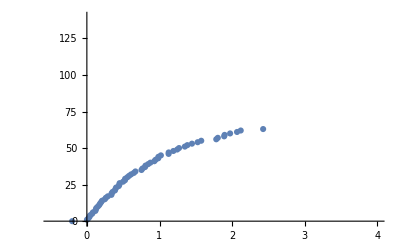

```mathematica
ListPlot[Transpose[{evs,ind}],PlotRange->{{-0.5,4},{-0.5,140}},PlotMarkers->Automatic]
```

```mathematica
gs=Sort[Transpose[Eigensystem[{ham,ov}]],#1[[1]]<#2[[1]]&][[1]]
```

{-0.202437,{-0.00111965,0.00404219,-0.00624711,0.00369016,0.00384502,-0.0130348,0.0202944,-0.0136028,-0.00695336,0.0218465,-0.0403655,0.0537586,0.00370691,-0.0101771,0.0520261,-0.305436,0.00404219,-0.0134656,0.0187643,-0.00708972,-0.0130348,0.0452519,-0.064466,0.0289542,0.0218465,-0.0718466,0.116904,-0.102111,-0.0101771,0.0258585,-0.0952424,0.481534,-0.00624711,0.0187643,-0.0253736,0.0214657,0.0202944,-0.064466,0.088165,-0.0511895,-0.0403655,0.116904,-0.158339,0.10107,0.0520261,-0.0952424,0.107397,-0.239732,0.00369016,-0.00708972,0.0214657,-0.10282,-0.0136028,0.0289542,-0.0511895,0.160955,0.0537586,-0.102111,0.10107,-0.101022,-0.305436,0.481534,-0.239732,0.117814}}

```mathematica
gs=gs[[2]]/Sqrt[gs[[2]].(ov.gs[[2]])]
```

{-0.0585666,0.211439,-0.326774,0.193025,0.201126,-0.681828,1.06156,-0.711536,-0.363717,1.14275,-2.11144,2.81201,0.193901,-0.532343,2.72139,-15.9768,0.211439,-0.70436,0.981525,-0.37085,-0.681828,2.36704,-3.37209,1.51454,1.14275,-3.75816,6.11503,-5.34125,-0.532343,1.35261,-4.98195,25.1881,-0.326774,0.981525,-1.32725,1.12283,1.06156,-3.37209,4.61174,-2.67763,-2.11144,6.11503,-8.2824,5.28679,2.72139,-4.98195,5.61771,-12.5399,0.193025,-0.37085,1.12283,-5.3783,-0.711536,1.51454,-2.67763,8.41926,2.81201,-5.34125,5.28679,-5.28427,-15.9768,25.1881,-12.5399,6.16264}

### L=1

```mathematica
Simplify[ctopm[{ca,cb,-ca-cb}]]
```

{-ca-cb,1/2 (-ca+cb)}

```mathematica
Solve[{ca+cb,1/2 (-ca+cb)}=={1,0}]
```

{{ca→1/2,cb→1/2}}

```mathematica
Solve[{1/3 (ca-2 (-ca-cb)+cb),1/2 (-ca+cb)}=={0,1}]
```

{{ca→-1,cb→1}}

```mathematica
cs={{1/2,1/2,-1},{-1,1,0}}
```

{{1/2,1/2,-1},{-1,1,0}}

```mathematica
ctopm/@cs
```

{{-1,0},{0,1}}

```mathematica
bs1=Block[{t},t=Table[-0.002 3.3^i, {i,5}];Flatten[Outer[List,t,t,t],2]];
```

```mathematica
matrixel1[{bs1[[1]],cs[[2]]},{bs1[[1]],cs[[1]]}]
```

{4.37387×10^-8,0.000640082}

```mathematica
bcs=Flatten[Outer[List,bs1,cs,1],1];
```

```mathematica
mm1=Outer[matrixel1[#1,#2,2.5]&,bcs,bcs,1];
```

```mathematica
ov1=Map[#[[1]]&,mm1,{2}];
```

```mathematica
Eigenvalues[ov1]
```

{47.7594,45.2857,22.029,20.2589,17.0157,12.28,8.72569,8.1543,7.95695,6.81745,6.17535,4.5559,3.53618,3.25238,3.14609,2.67224,2.56208,2.51125,1.91694,1.89454,1.72708,1.68312,1.26162,1.2258,1.05563,0.978147,0.912956,0.835139,0.825214,0.683965,0.623878,0.592914,0.573569,0.518382,0.517271,0.456493,0.418206,0.385251,0.379306,0.376137,0.353343,0.351713,0.295624,0.278216,0.247423,0.2247,0.214419,0.195561,0.186611,0.180168,0.166698,0.154417,0.143937,0.13819,0.128592,0.12049,0.118386,0.105994,0.100019,0.0920421,0.0853453,0.0845179,0.0771928,0.0710931,0.069619,0.0682447,0.0612045,0.0578652,0.0543731,0.0530162,0.0528133,0.0468621,0.0445151,0.0436393,0.0429661,0.0411968,0.0392638,0.0361001,0.0335292,0.0307107,0.0298775,0.0262511,0.0260268,0.0236693,0.0223443,0.0221201,0.020356,0.0199888,0.0188994,0.01753,0.0173222,0.0166584,0.0161696,0.014626,0.0135947,0.0135666,0.0127654,0.0119926,0.0110855,0.010509,0.0103838,0.0100894,0.00989591,0.00853286,0.008197,0.00765534,0.00756721,0.00719126,0.00687083,0.00643982,0.00643326,0.00582046,0.00550669,0.00545168,0.00513015,0.00504206,0.00475159,0.00460059,0.00439674,0.00396462,0.00387747,0.00376649,0.00374009,0.00335656,0.00305921,0.00292246,0.00286349,0.00277079,0.00255446,0.00217118,0.00212796,0.0019989,0.0019283,0.00180588,0.00177239,0.00176981,0.00163455,0.00150252,0.00148397,0.00146603,0.00144686,0.00142714,0.00140475,0.00124563,0.0011007,0.00108102,0.000952734,0.000885375,0.00088394,0.00081832,0.000739699,0.000720145,0.000670541,0.000662747,0.000642805,0.000632127,0.000600922,0.000591266,0.000581983,0.00051642,0.000500986,0.00046538,0.000460063,0.000447693,0.000393374,0.000374884,0.000346084,0.000327786,0.000314097,0.000274776,0.00025371,0.000239253,0.000223927,0.000208962,0.000195884,0.000190465,0.000178682,0.00017747,0.000172654,0.000172011,0.000139486,0.000127889,0.000115764,0.000111718,0.000107248,0.0000967413,0.0000950352,0.0000929176,0.0000879394,0.0000840851,0.0000718743,0.0000711477,0.000065123,0.0000512937,0.0000486777,0.0000468001,0.0000415648,0.0000411191,0.0000387086,0.0000375658,0.000033473,0.0000311939,0.0000307522,0.0000293022,0.000027718,0.0000251752,0.0000236613,0.0000205748,0.0000200039,0.0000192166,0.0000179878,0.0000169393,0.0000160559,0.0000159176,0.0000126487,0.0000111986,8.59982×10^-6,7.97417×10^-6,7.81318×10^-6,7.4593×10^-6,7.2281×10^-6,6.18528×10^-6,6.07201×10^-6,5.39712×10^-6,4.96255×10^-6,3.43645×10^-6,2.63336×10^-6,2.42771×10^-6,1.96961×10^-6,1.74454×10^-6,1.39797×10^-6,1.2649×10^-6,1.15064×10^-6,1.0396×10^-6,9.26384×10^-7,7.18037×10^-7,6.85295×10^-7,6.35256×10^-7,2.57928×10^-7,1.93114×10^-7,1.61134×10^-7,1.52442×10^-7,1.06712×10^-7,9.59344×10^-8,2.9112×10^-8,2.3284×10^-8,1.74834×10^-8,7.85479×10^-9,4.67006×10^-9,4.51237×10^-9}

```mathematica
ham1=Map[#[[2]]&,mm1,{2}];
```

```mathematica
ev1=Sort[Eigenvalues[{ham1,ov1}]]
```

{-0.036502,-0.0329525,0.00156126,0.0153634,0.0325695,0.0388505,0.0716742,0.0732093,0.0849643,0.0888585,0.0967028,0.103223,0.108083,0.110383,0.133904,0.15477,0.15567,0.155836,0.170703,0.180693,0.196678,0.205556,0.215342,0.245683,0.25349,0.25889,0.261221,0.275824,0.284623,0.293229,0.322815,0.333306,0.335951,0.337804,0.338475,0.35075,0.359742,0.370498,0.393924,0.415324,0.418929,0.427644,0.434929,0.442259,0.460948,0.462129,0.467349,0.481614,0.527361,0.532806,0.541414,0.54632,0.566174,0.590901,0.61571,0.62494,0.638501,0.643604,0.653832,0.662572,0.707062,0.708178,0.76126,0.783669,0.796459,0.80066,0.830595,0.839456,0.846296,0.861094,0.867298,0.88869,0.889054,0.897615,0.903305,0.923344,0.947778,0.965501,0.96559,0.977662,0.984274,1.00033,1.01535,1.08594,1.10335,1.11015,1.12112,1.12601,1.1696,1.1722,1.18355,1.19176,1.19604,1.21795,1.25089,1.27709,1.29352,1.29631,1.34635,1.35236,1.37442,1.43115,1.44401,1.45653,1.46935,1.47878,1.51893,1.5218,1.54043,1.55485,1.61199,1.61691,1.64162,1.64395,1.67804,1.68984,1.7403,1.76628,1.79093,1.85386,1.86712,1.88047,1.92856,2.02392,2.02831,2.04059,2.06404,2.07018,2.10624,2.13782,2.14591,2.15658,2.1574,2.23586,2.28815,2.30397,2.32216,2.33329,2.35388,2.37599,2.37957,2.42461,2.43277,2.43833,2.45124,2.4789,2.51737,2.52608,2.56901,2.58863,2.6197,2.62761,2.62946,2.65212,2.6655,2.69019,2.75154,2.76993,2.79889,2.81552,2.85302,2.87195,2.95098,2.95209,3.06703,3.13614,3.16706,3.19002,3.22142,3.2538,3.26869,3.28465,3.32478,3.35588,3.36593,3.39279,3.41576,3.43874,3.4999,3.50575,3.53121,3.5445,3.6191,3.62334,3.62938,3.67979,3.72454,3.79861,3.84262,3.87677,3.91834,3.92202,3.96694,3.98499,4.06004,4.13263,4.14178,4.25666,4.29157,4.36706,4.43987,4.44867,4.47186,4.59961,4.64019,4.68099,4.77032,4.77823,4.80663,4.83641,4.89902,4.90163,4.98548,5.15568,5.23199,5.48105,5.51369,5.5891,5.68608,5.73197,5.80531,5.82174,5.8578,5.88436,6.18104,6.21691,6.40663,6.44216,6.53535,6.62085,6.64916,6.65772,7.18718,7.29204,7.33581,7.63605,7.67363,7.76435,7.84231,8.3875,8.45372,8.70599,8.82871,8.93062,9.0226,9.36448,9.43605,9.54753,9.58112,9.6622}

```mathematica
ind=Table[i,{i,Length[ev1]}]-1;
```

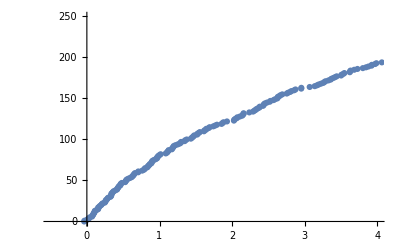

```mathematica
ListPlot[Transpose[{ev1,ind}],PlotRange->{{-0.5,4},{-0.5,250}},PlotMarkers->Automatic]
```

## LIT

```mathematica
Clear[ovl];ovl[bc_,bp_,debug_:False]:=Block[{α,β,γ,αp,βp,γp,bs,αs,βs,γs,cp,cm,cpp,cpm,ovl,ovl0,kin,pot, s,λ0=1.4,v2},
bs=bc[[1]]+bp;
{α,β,γ}=αβγ[bc[[1]]];{αp,βp,γp}=αβγ[bp]; {αs,βs,γs}=αβγ[bs];
{cp,cm}=ctopm[bc[[2]]];{cpp,cpm}={2/3,0};

ovl0=  (dαβγ[2α,2β,2γ]^(3/4)dαβγ[2αp,2βp,2γp]^(3/4))/dαβγ[αs,βs,γs]^(3/2)/(dαβγc[2α,2β,2γ,cm cm,cp cp,2cm cp]^(1/2));
ovl0
dαβγc[α+αp,β+βp,γ+γp,cm cpm,cp cpp,cpm cp+cm cpp]
]
```

```mathematica
ovmat=Outer[ovl[#1,#2]&,bcs,bs,1];
```

```mathematica
rhs=ovmat.gs
```

{-0.0807649,0.00801309,-0.125807,0.0129152,-0.172749,0.0222058,-0.186589,0.022547,-0.14764,0.0137438,-0.14006,0.00491269,-0.223416,0.00372703,-0.312255,0.00784916,-0.334793,0.00798375,-0.262294,0.0049803,-0.162608,-0.0140871,-0.29622,-0.0305845,-0.477173,-0.0408313,-0.570094,-0.035043,-0.477982,-0.0215375,-0.113083,-0.0327098,-0.228032,-0.0610608,-0.445333,-0.104528,-0.632032,-0.114722,-0.59573,-0.0786211,-0.055755,-0.0304457,-0.112523,-0.0550459,-0.252751,-0.111265,-0.423737,-0.150053,-0.464433,-0.125482,-0.148287,0.0189797,-0.230509,0.0355398,-0.319426,0.0516428,-0.338686,0.0462431,-0.263659,0.0255889,-0.253858,0.0170363,-0.331168,0.0260242,-0.425624,0.0354936,-0.450584,0.0322802,-0.356201,0.018195,-0.316008,-0.015962,-0.412549,-0.0184767,-0.554305,-0.0201701,-0.621642,-0.0140005,-0.515168,-0.00838192,-0.230072,-0.0538267,-0.323368,-0.0723709,-0.498808,-0.0995171,-0.650427,-0.102056,-0.599991,-0.0685016,-0.11172,-0.0532215,-0.164665,-0.0758178,-0.283167,-0.117544,-0.432182,-0.146116,-0.463561,-0.120781,-0.192395,0.0476869,-0.33116,0.0843252,-0.508862,0.123167,-0.584996,0.116147,-0.481873,0.0693581,-0.347163,0.0644545,-0.445076,0.0848301,-0.580604,0.108905,-0.634365,0.0999156,-0.518623,0.0598515,-0.521965,0.0343305,-0.579293,0.0398728,-0.671098,0.0480112,-0.710579,0.0465031,-0.586279,0.0292131,-0.462141,-0.058699,-0.509868,-0.0624296,-0.604412,-0.0671148,-0.683582,-0.0599961,-0.605557,-0.038616,-0.250153,-0.0970219,-0.281199,-0.105745,-0.354618,-0.123005,-0.451923,-0.131294,-0.45953,-0.10608,-0.161405,0.0721543,-0.300197,0.125215,-0.535454,0.202685,-0.692594,0.214916,-0.617105,0.142287,-0.301499,0.11392,-0.407668,0.150152,-0.586828,0.200178,-0.706712,0.201087,-0.620186,0.132139,-0.541028,0.1409,-0.587522,0.151114,-0.672706,0.165505,-0.725709,0.154636,-0.621439,0.101275,-0.623261,0.0383373,-0.637072,0.0394976,-0.66539,0.0415255,-0.679719,0.0402469,-0.585898,0.0276539,-0.412098,-0.0867517,-0.420964,-0.0870832,-0.442768,-0.0869754,-0.470903,-0.0824268,-0.438394,-0.0656564,-0.0999219,0.0661381,-0.187163,0.114939,-0.366974,0.202881,-0.530781,0.241863,-0.517652,0.181565,-0.185614,0.111316,-0.258279,0.149453,-0.400707,0.210905,-0.536263,0.235439,-0.514913,0.175347,-0.360717,0.18015,-0.395498,0.192401,-0.470127,0.213367,-0.545403,0.212409,-0.504851,0.155892,-0.497952,0.154656,-0.504896,0.154757,-0.520198,0.153125,-0.52973,0.140725,-0.466552,0.102908,-0.41726,0.0156266,-0.41726,0.0155077,-0.416236,0.0150801,-0.405788,0.0135383,-0.352275,0.00943636}

```mathematica
es=Eigensystem[{ham1,ov1}];
```

```mathematica
evs=Table[es[[2,i]]/Sqrt[es[[2,i]].ov1.es[[2,i]]],{i,Length[es[[1]]]}]
```

{{0.00983158,-0.00916279,-0.0393837,0.0351843,0.0701022,-0.096531,-0.0973128,0.133967,0.037329,-0.135941,-0.0458448,0.0490484,0.161643,-0.163977,-0.310228,0.349184,218,-84.5749,-18.3143,23.3848,-21.908,23.6396,-113.653,-347.56,1099.79,507.282,-1635.98,-175.428,616.892,7.87866,-74.3185,-2.27169,13.9945},248,{1}}
 |  |  |  |

```mathematica
Length[evs[[1]]]
```

250

```mathematica
Sort[Transpose[es],#⟦1⟧<#2⟦1⟧&][[;;2]]
```

{{-0.036502,{-0.0142931,0.00825214,0.00164177,-0.00460728,-0.0582549,0.000636952,-0.00943323,0.000207058,-0.0488555,-0.0000728978,0.00945889,-0.00680822,-0.010948,0.00268299,0.0427653,0.00529051,-0.000947067,-0.0209843,0.0359627,0.0219513,-0.00178743,0.00154615,0.00160795,0.00355428,-0.011712,-0.00986089,-0.0272559,0.0502763,0.0626055,-0.0683754,-0.000880706,0.00083654,0.00251761,-0.00552712,-0.00234715,0.0129504,-0.00504528,-0.0150538,-0.106359,0.0431864,0.000582433,-0.000572924,-0.00135208,0.00312082,0.0070291,-0.0141978,0.00601328,-0.00529493,-0.174709,0.256479,0.00529952,0.00206804,-0.0136734,0.00677769,0.0474669,-0.00516337,-0.004274,0.0188945,0.0377827,-0.0212857,-0.00636664,0.00842297,0.0245898,-0.0141965,-0.0767878,0.00312768,0.019927,0.0017169,-0.0862654,-0.000460095,-0.00151354,-0.00375513,-0.00644826,0.00464096,0.0362423,0.00515879,0.0226222,-0.0669027,-0.0495976,0.098844,0.00415907,-0.000492421,-0.00475402,0.00411209,-0.00202167,-0.016458,0.00963677,0.0279294,0.152263,-0.0803649,-0.00225931,0.000367805,0.0023445,-0.00222696,-0.00870972,0.0210462,-0.00997404,0.00230362,0.253561,-0.369768,-0.0180993,0.0438634,0.0234201,-0.0311955,-0.0280723,0.0129998,-0.0158316,-0.0449969,0.0543851,0.0629354,0.00774159,-0.0397345,-0.0315572,0.0589694,0.0593349,-0.0294127,0.0051025,0.0628578,-0.0361686,-0.0910444,0.00326736,0.0176835,0.0100533,-0.0365813,-0.0439111,0.0253527,0.00466081,-0.00372631,0.00481937,-0.00287953,-0.00852824,-0.00460586,0.00931737,0.0112715,0.00786065,-0.00565896,-0.00855619,-0.00835953,-0.0504183,0.0407953,0.0106789,-0.00200655,-0.0154295,0.000712098,0.00801109,-0.00692994,0.00301656,0.00420722,-0.0879926,0.125793,-0.0029678,0.00667863,-0.033503,-0.0244867,0.0528463,0.0512214,-0.0226923,0.0102599,-0.107187,-0.0457618,0.0330138,0.0324248,0.0034662,-0.0173614,-0.0740704,-0.0560744,0.0420803,-0.0194861,0.147226,0.0831498,-0.0597618,-0.0274607,0.0757726,0.0422882,0.00551804,-0.000987344,-0.0200052,0.00991748,-0.0442551,-0.039792,0.00915124,0.0152702,-0.017274,-0.0279565,0.00323183,0.0130604,0.0052946,-0.00305794,0.00909406,-0.000739929,0.00537815,-0.00390587,-0.00530879,0.0101231,-0.00132069,-0.00570499,0.000923217,-0.000662844,0.0090671,-0.0133848,-0.0121551,0.0370012,0.0690916,0.027796,-0.100824,-0.140259,0.0226766,0.118974,0.037868,-0.0172145,-0.0501687,-0.08566,-0.0218087,0.0661398,0.144926,0.160516,-0.0552987,-0.180922,-0.0502983,0.0230675,0.130945,0.0643511,-0.170119,-0.110985,0.00548487,-0.000178662,0.0320577,0.0661871,0.0128962,-0.00608765,-0.074267,0.0436016,0.126474,-0.045624,-0.0574569,0.00415477,0.00410818,-0.00671615,-0.00162954,0.000821229,-0.238045,-0.0150815,0.347527,0.018147,-0.122755,-0.00245208,0.0140533,-0.0000557399,-0.000976305,0.000562244}},{-0.0329525,{0.00615515,0.0106611,0.0142463,-0.0057637,0.0651109,0.00085646,0.0159825,0.0000765598,0.0613171,-0.0000340896,-0.00541924,-0.011702,-0.00163558,0.0156699,-0.046678,-0.0110997,-0.0037323,0.0245102,-0.0478142,-0.024408,0.00253665,0.00658292,0.00239183,-0.0152544,0.00857042,0.0216507,0.0289654,-0.0568327,-0.0557408,0.0706199,-0.000729937,-0.00208057,-0.00205277,0.00673915,-0.00156645,-0.0128544,-0.0179346,0.0606859,0.149757,-0.0737637,0.00016613,0.00049061,0.00084575,-0.00188508,0.000228155,0.000864644,-0.0236845,-0.000700132,0.0498758,-0.0673715,-0.0111344,0.00714029,-0.0047693,-0.00709231,-0.0406771,0.0120036,-0.00815242,-0.0265,-0.0456429,0.0249797,0.0129377,0.0082003,-0.0073745,-0.0127736,0.0665313,0.00151156,-0.00526251,0.00188103,0.0990222,-0.000452429,-0.010452,-0.00563436,0.00846742,0.0182846,-0.0281376,-0.02752,-0.0290572,0.0741189,0.0345236,-0.0994481,0.00459868,0.000749662,-0.0023535,-0.00610827,0.0090517,0.0157396,0.023308,-0.0945309,-0.212018,0.125006,-0.00137819,0.000263387,0.00057963,0.00165563,-0.0020922,-0.0000542672,0.0353997,0.00657521,-0.0613892,0.0786213,-0.018019,0.0509378,0.0292232,-0.0204322,-0.0121641,-0.0168986,0.0433134,0.0603035,-0.0646907,-0.0748252,0.00297338,-0.0482071,-0.0230416,0.0541887,0.00176707,0.00262858,-0.0510218,-0.0757967,0.048923,0.105435,0.0130191,0.0227086,-0.010656,-0.0429676,0.01484,0.0257018,0.0210036,-0.00453375,-0.00299173,-0.00215825,-0.00691962,-0.00903042,0.00588507,0.0188108,-0.00679418,-0.0146639,-0.0100154,0.0399857,0.0692172,-0.0561973,0.000353193,0.000754476,0.00094462,-0.00280573,0.0000971138,0.000261928,-0.0124674,-0.00713042,0.0105793,-0.00752765,-0.00406202,0.0122334,-0.0428721,-0.0449431,0.0628794,0.0847984,-0.0574759,-0.0779619,0.160122,0.0654537,0.039869,0.0341375,0.00420575,-0.00173808,-0.0730762,-0.101173,0.088288,0.122653,-0.234311,-0.113059,-0.0670281,-0.0325621,0.0851775,0.0435902,-0.012377,0.0134373,-0.0325495,-0.0484088,0.0825131,0.0531793,0.0492974,0.0253666,-0.0775414,-0.0420729,0.0352883,0.0155482,-0.0000449586,-0.0000749679,-0.0170088,-0.000331182,0.00874354,-0.0275753,-0.0101408,0.0441417,0.000869007,-0.0179346,0.00156413,0.00336173,0.0020993,-0.00395096,-0.015749,0.0459536,0.081424,0.0316415,-0.119858,-0.166774,0.0300626,0.175167,0.13625,0.183192,-0.0537771,-0.101171,-0.0272491,0.0738154,0.165773,0.191149,-0.0630271,-0.271028,-0.177796,-0.24085,0.132903,0.0733621,-0.166999,-0.123529,-0.00214805,-0.00491477,0.0344221,0.105962,0.041221,0.0571607,-0.118007,0.0481311,0.189669,-0.0505206,-0.0790779,0.00553455,0.00593414,-0.0138254,0.000803279,0.00120431,-0.0640653,0.00055247,0.0767258,-0.0042638,-0.00932661,0.00519162,-0.00389759,-0.000546463,-0.000113534,-0.000194115}}}

```mathematica
Sort[Transpose[{es[[1]],(#.rhs)^2&/@evs}],#⟦1⟧<#2⟦1⟧&]
```

{{-0.036502,0.0242846},{-0.0329525,0.00125321},{0.00156126,0.0874523},{0.0153634,0.00700572},{0.0325695,9.85871×10^-6},{0.0388505,0.000173222},{0.0716742,0.0000121844},{0.0732093,0.163241},{0.0849643,2.53461×10^-9},{0.0888585,0.00429558},{0.0967028,0.000887996},{0.103223,0.0188508},{0.108083,0.00230771},{0.110383,0.000303284},{0.133904,0.0000490806},{0.15477,0.00238325},{0.15567,0.000416471},{0.155836,0.0000155103},{0.170703,6.09038×10^-7},{0.180693,0.0000376284},{0.196678,0.000647039},{0.205556,0.133248},{0.215342,0.00760578},{0.245683,0.000120035},{0.25349,0.00260106},{0.25889,5.2702×10^-6},{0.261221,0.0232439},{0.275824,0.00529338},{0.284623,0.000880549},{0.293229,0.0000233748},{0.322815,0.000343473},{0.333306,0.000780868},{0.335951,0.000824381},{0.337804,3.36638×10^-6},{0.338475,0.00321619},{0.35075,0.000696705},{0.359742,0.0000115218},{0.370498,0.0000309956},{0.393924,0.000118301},{0.415324,0.0162686},{0.418929,0.00165383},{0.427644,0.0289073},{0.434929,0.00536767},{0.442259,0.000013806},{0.460948,0.0251933},{0.462129,0.000280644},{0.467349,0.00161379},{0.481614,0.016699},{0.527361,0.00235913},{0.532806,0.000011363},{0.541414,0.00345271},{0.54632,0.0000391139},{0.566174,0.00582535},{0.590901,0.00187151},{0.61571,0.000117857},{0.62494,0.000880132},{0.638501,0.0000286383},{0.643604,0.00105669},{0.653832,0.0000805076},{0.662572,0.000144924},{0.707062,7.88572×10^-6},{0.708178,0.000275703},{0.76126,0.000233301},{0.783669,0.00205812},{0.796459,0.000192946},{0.80066,0.00224643},{0.830595,5.14116×10^-6},{0.839456,0.00662294},{0.846296,0.022393},{0.861094,0.000274763},{0.867298,0.00379745},{0.88869,0.000520069},{0.889054,0.000599553},{0.897615,0.000480469},{0.903305,0.00106571},{0.923344,0.000234209},{0.947778,0.00116979},{0.965501,0.000382875},{0.96559,0.00720065},{0.977662,0.0000650176},{0.984274,0.00109778},{1.00033,0.0000671515},{1.01535,0.00555587},{1.08594,0.0000125812},{1.10335,0.000538311},{1.11015,1.38217×10^-7},{1.12112,0.000334111},{1.12601,0.000227716},{1.1696,0.000209151},{1.1722,0.000489712},{1.18355,0.000757685},{1.19176,0.000456365},{1.19604,0.0000413171},{1.21795,1.33343×10^-6},{1.25089,0.0000986065},{1.27709,8.72384×10^-6},{1.29352,6.73551×10^-6},{1.29631,0.0000172378},{1.34635,4.68694×10^-8},{1.35236,0.0000225142},{1.37442,5.38364×10^-8},{1.43115,0.0000227792},{1.44401,0.0000852604},{1.45653,0.0000694226},{1.46935,0.000268856},{1.47878,0.0000527104},{1.51893,0.000498871},{1.5218,0.000380328},{1.54043,0.000120596},{1.55485,0.00114798},{1.61199,0.0000672603},{1.61691,0.0000725518},{1.64162,0.000398775},{1.64395,3.09074×10^-6},{1.67804,0.0000368956},{1.68984,0.000117031},{1.7403,0.00012063},{1.76628,0.000662052},{1.79093,0.0000290139},{1.85386,0.000014861},{1.86712,0.00121087},{1.88047,0.0000330322},{1.92856,0.000206215},{2.02392,0.0000191709},{2.02831,0.00116484},{2.04059,0.00624919},{2.06404,0.000626472},{2.07018,0.000563129},{2.10624,0.00145742},{2.13782,0.00151323},{2.14591,0.0000107739},{2.15658,0.00308581},{2.1574,1.36229×10^-7},{2.23586,0.000366046},{2.28815,0.000908752},{2.30397,4.41974×10^-6},{2.32216,0.0000769253},{2.33329,0.000451156},{2.35388,0.0000106602},{2.37599,0.00122585},{2.37957,0.000160718},{2.42461,0.000042149},{2.43277,0.00277586},{2.43833,0.0000141628},{2.45124,0.000192528},{2.4789,0.0000987941},{2.51737,0.000678417},{2.52608,0.000112849},{2.56901,0.000132909},{2.58863,4.38128×10^-6},{2.6197,0.0000122},{2.62761,0.000291095},{2.62946,0.0000871884},{2.65212,0.000105585},{2.6655,0.000293807},{2.69019,0.000360955},{2.75154,0.0000417259},{2.76993,0.000148204},{2.79889,0.000338154},{2.81552,0.0000132934},{2.85302,1.22624×10^-6},{2.87195,0.0000809544},{2.95098,0.0000223964},{2.95209,0.000183692},{3.06703,0.000168018},{3.13614,0.0000102905},{3.16706,0.000234625},{3.19002,0.000037256},{3.22142,0.0000122016},{3.2538,0.0000480624},{3.26869,4.17838×10^-6},{3.28465,0.000142965},{3.32478,0.00010542},{3.35588,0.000826061},{3.36593,0.0000859768},{3.39279,0.000116476},{3.41576,0.0000433601},{3.43874,0.00043264},{3.4999,0.0000132421},{3.50575,0.000254393},{3.53121,0.0000127773},{3.5445,0.000013032},{3.6191,0.000640256},{3.62334,3.52927×10^-7},{3.62938,1.11683×10^-6},{3.67979,0.000177483},{3.72454,0.000706147},{3.79861,1.34553×10^-6},{3.84262,0.0000194705},{3.87677,0.0000418028},{3.91834,0.0000191037},{3.92202,0.000282647},{3.96694,0.000541712},{3.98499,0.000183255},{4.06004,4.79152×10^-6},{4.13263,0.000241268},{4.14178,6.71116×10^-6},{4.25666,8.32354×10^-6},{4.29157,0.0000248976},{4.36706,1.70474×10^-7},{4.43987,0.0000364472},{4.44867,4.05483×10^-6},{4.47186,0.000110031},{4.59961,0.0000108252},{4.64019,0.0000215571},{4.68099,0.0000572436},{4.77032,0.000365315},{4.77823,2.42866×10^-6},{4.80663,0.000188427},{4.83641,0.0000445546},{4.89902,0.000117031},{4.90163,2.59084×10^-6},{4.98548,1.91215×10^-6},{5.15568,0.000681139},{5.23199,0.000417611},{5.48105,9.62099×10^-6},{5.51369,0.000257798},{5.5891,4.9469×10^-7},{5.68608,1.91305×10^-6},{5.73197,6.35489×10^-6},{5.80531,1.20033×10^-7},{5.82174,0.000040024},{5.8578,0.0000290616},{5.88436,1.78183×10^-6},{6.18104,8.84273×10^-8},{6.21691,0.000388766},{6.40663,0.000330878},{6.44216,0.000111912},{6.53535,8.82811×10^-7},{6.62085,0.000119861},{6.64916,0.0000133733},{6.65772,0.0000372452},{7.18718,8.3721×10^-6},{7.29204,0.0000375253},{7.33581,1.53357×10^-6},{7.63605,0.0000923022},{7.67363,6.40634×10^-6},{7.76435,0.0000143899},{7.84231,2.51726×10^-6},{8.3875,7.74575×10^-6},{8.45372,0.0000184696},{8.70599,1.6765×10^-6},{8.82871,4.02418×10^-6},{8.93062,0.0000129235},{9.0226,2.72181×10^-6},{9.36448,0.0000246622},{9.43605,0.000136246},{9.54753,0.000025643},{9.58112,0.0000623122},{9.6622,9.57642×10^-6}}

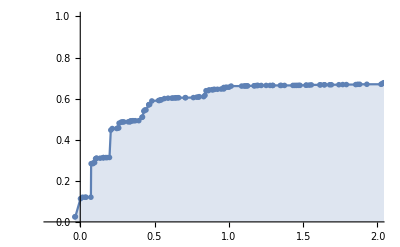

```mathematica
sm=0;ListLinePlot[{#[[1]],sm+=#[[2]]}&/@Sort[Transpose[{es[[1]],(#.rhs)^2&/@evs}],#⟦1⟧<#2⟦1⟧&],PlotMarkers->"OpenMarkers",Filling->Axis,PlotRange->{{-0.2,2},{0,1}}]
```